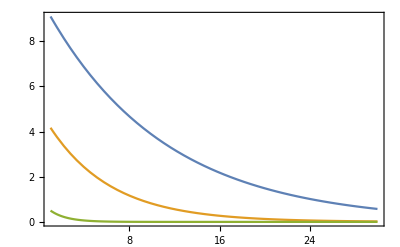

```mathematica
FCP=(ⅇ^(-r T)γ^-T)/(ⅇ^r γ-1) ;
Plot[{FCP/. {γ->1.1,r->0},FCP /. {γ->1.2,r->0},FCP /. {γ->2,r->0}},{T,1,30},PlotRange->All,Frame->True,BaseStyle->{FontSize->14}]
```

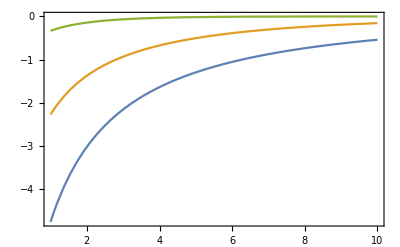

```mathematica
ROI=ⅇ^(-r (T+1))/(ⅇ^(r(T+1))-γ^(T+1)) ;
Plot[{ROI/. {γ->1.1,r->0},ROI /. {γ->1.2,r->0},ROI /. {γ->2,r->0}},{T,1,10},PlotRange->All,Frame->True,BaseStyle->{FontSize->14}]
```

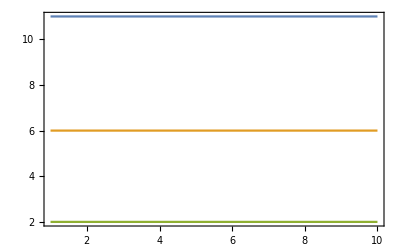

```mathematica
QAP=(ⅇ^r γ)/(ⅇ^r γ-1) ;
Plot[{QAP/. {γ->1.1,r->0},QAP /. {γ->1.2,r->0},QAP /. {γ->2,r->0}},{T,1,10},PlotRange->All,Frame->True,BaseStyle->{FontSize->14}]
```

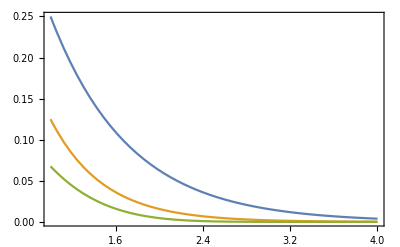

```mathematica
Plot[{1/(gN^t gC^t)/. {gN->2,gC->2},1/(gN^(2t)gC^t)/. {gN->2,gC->2},1/(Exp[gN^t] gC^t)/. {gN->2,gC->2}},{t,1,4},PlotRange->All,Frame->True,BaseStyle->{FontSize->14}]
```